# Just launch the code below to run the notebook (shift+enter)

```mathematica
ClearAll["Global`*"]
BlockEvaluation[tag_]:=Block[{},
nb=EvaluationNotebook[];
NotebookFind[nb,tag,All,CellTags];
SelectionEvaluate[nb]
]
dropdownDialog[list_,phrase_]:=DialogInput[{choice=""},Column[{TextCell[phrase],PopupMenu[Dynamic[choice],list],Button["OK",DialogReturn[choice]]}]]
infoDialog[phrase_]:=DialogInput[{choice=""},Column[{TextCell[phrase],Button["Proceed",DialogReturn[choice]]}]]
If[(DirectoryQ[FileNameJoin[{NotebookDirectory[],"Auxiliary data"}]]//ToString)=="False",CreateDirectory[FileNameJoin[{NotebookDirectory[],"Auxiliary data"}]]];
If[(DirectoryQ[FileNameJoin[{NotebookDirectory[],"Auxiliary data/ALPs with photon coupling"}]]//ToString)=="False",CreateDirectory[FileNameJoin[{NotebookDirectory[],"Auxiliary data/ALPs with photon coupling"}]]];
choiceslist={"Acceptance","Tabulated number of events","Sensitivity"};
taglist["Acceptance"]="Acceptance";
taglist["Tabulated number of events"]="Number-of-events";
taglist["Sensitivity"]="Sensitivity";
computationchoice=dropdownDialog[choiceslist,"Do you want to compute acceptance, tabulated number of events, or sensitivity (if the tabulated number of events has been already produced)?"];
tagselected=taglist[computationchoice]
BlockEvaluation[tagselected]
```

# Preliminary definitions (launch first)

## ALP phenomenology

## ALP lifetime and production branching ratios

### Production branching ratios

```mathematica
Brπ0ToALP[ma_]=If[ma<0.135,Evaluate[Interpolation[Import[FileNameJoin[{NotebookDirectory[],"phenomenology/ALPs with photon coupling/branching ratios/BrPi0ToALP.txt"}],"Table"],InterpolationOrder->1][ma]],0];
BrηToALP[ma_]=If[ma<0.547,Evaluate[Interpolation[Import[FileNameJoin[{NotebookDirectory[],"phenomenology/ALPs with photon coupling/branching ratios/BrEtaToALP.txt"}],"Table"],InterpolationOrder->1][ma]],0];
```

### ALP lifetime

```mathematica
<<FeynCalc`
(*1/4 1/2 from the definition of the Lagrangian, 2 from combinatorics*)
MALPdecay=ga/4 1/2*2*LeviCivita[μ,ν,α,β]*(FV[pγ1,μ]*PolarizationVector[pγ1,ν]-FV[pγ1,ν]*PolarizationVector[pγ1,μ])(FV[pγ2,α]*PolarizationVector[pγ2,β]-FV[pγ2,β]*PolarizationVector[pγ2,α])//Contract//Simplify;
MALPdecayStar = ComplexConjugate[MALPdecay];
MALPdecaySquared=(DoPolarizationSums[DoPolarizationSums[MALPdecay MALPdecayStar,pγ1],pγ2]//Contract//Simplify)/.{ScalarProduct[pγ1,pγ2]->ma^2/2,ScalarProduct[pγ1,pγ1]->0,ScalarProduct[pγ2,pγ2]-> 0}//Simplify;
Print["ALP decay width:"]
(*chbar*)
chbar= 6.6*10^-25*3*10^8;
(*1/2 from indistinguishability of two photons*)
ΓALPdecay[ma_,ga_]=1/(8Pi)*1/2 MALPdecaySquared*1/(2ma);
cτALPphoton[ma_,ga_]=chbar/ΓALPdecay[ma,ga]
ldecayALPphoton[ma_,ga_,Ea_]=cτALPphoton[ma,ga]*(√(Ea^2-ma^2))/ma;
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

ALP decay width:

(3.98103×10^-14)/(ga^2 ma^3)

## Compilable interpolation function mapping one grid into another

## 3D to 3D

```mathematica
nd=3;
cf3=Module[{xgvars=Unique["xg"]&/@slist@@Range@nd,igvars=Unique["ig"]&/@slist@@Range@nd,tgvars=Unique["tg"]&/@slist@@Range@nd,ivars=Unique["i"]&/@slist@@Range@nd,svars=Unique["s"]&/@slist@@Range@nd,tvars=Unique["t"]&/@slist@@Range@nd,jvars=Unique["j"]&/@slist@@Range@nd},Inactivate[Compile[{seq@{xgvars,_Real,1},{y,_Real,nd}},Module[{seq@igvars,seq@tgvars,seq@ivars,seq@svars,seq@tvars},seq[igvars=Floor[xgvars]-UnitStep[xgvars-indexed@Dimensions@y]];
seq[tgvars=xgvars-igvars];
Table[seq[tvars=Compile`GetElement[tgvars,jvars]];
seq[ivars=Compile`GetElement[igvars,jvars]];
seq[svars=1.-tvars];
eval@Total[Times@@#[[All,1]] Compile`GetElement[y,Sequence@@#[[All,2]]]&/@Tuples@Transpose[{{svars,ivars},{tvars,ivars+1}},{2,3,1}]],seq@{jvars,Length@igvars}]],CompilationTarget->"C",RuntimeAttributes->{Listable},Parallelization->True,RuntimeOptions->"Speed"],Except[seq|eval|indexed]]/.seq[expr_]:>RuleCondition@(Sequence@@Table[Inactivate[expr,Except[slist|indexed]]/.{l_slist:>l[[i]],indexed[l_]:>Inactive[Compile`GetElement][l,i]},{i,nd}])/.eval@expr_:>RuleCondition[Activate[expr/.slist->List]]]//Activate;
```

## 4D to 4D

```mathematica
nd=4;
cf4=Module[{xgvars=Unique["xg"]&/@slist@@Range@nd,igvars=Unique["ig"]&/@slist@@Range@nd,tgvars=Unique["tg"]&/@slist@@Range@nd,ivars=Unique["i"]&/@slist@@Range@nd,svars=Unique["s"]&/@slist@@Range@nd,tvars=Unique["t"]&/@slist@@Range@nd,jvars=Unique["j"]&/@slist@@Range@nd},Inactivate[Compile[{seq@{xgvars,_Real,1},{y,_Real,nd}},Module[{seq@igvars,seq@tgvars,seq@ivars,seq@svars,seq@tvars},seq[igvars=Floor[xgvars]-UnitStep[xgvars-indexed@Dimensions@y]];
seq[tgvars=xgvars-igvars];
Table[seq[tvars=Compile`GetElement[tgvars,jvars]];
seq[ivars=Compile`GetElement[igvars,jvars]];
seq[svars=1.-tvars];
eval@Total[Times@@#[[All,1]] Compile`GetElement[y,Sequence@@#[[All,2]]]&/@Tuples@Transpose[{{svars,ivars},{tvars,ivars+1}},{2,3,1}]],seq@{jvars,Length@igvars}]],CompilationTarget->"C",RuntimeAttributes->{Listable},Parallelization->True,RuntimeOptions->"Speed"],Except[seq|eval|indexed]]/.seq[expr_]:>RuleCondition@(Sequence@@Table[Inactivate[expr,Except[slist|indexed]]/.{l_slist:>l[[i]],indexed[l_]:>Inactive[Compile`GetElement][l,i]},{i,nd}])/.eval@expr_:>RuleCondition[Activate[expr/.slist->List]]]//Activate;
```

# Specifying the experiment

```mathematica
SetDirectory[NotebookDirectory[]];
(*Parent directory*)
NotebookDirectory[]//ParentDirectory;
AcceptanceDirectory=FileNameJoin[{NotebookDirectory[],"Acceptances"}];
ExperimentDirectoriesList=Select[FileNames["*",AcceptanceDirectory,1],DirectoryQ];
(*List of available experiments (for which the geometry has been implemented)*)
ExperimentsListTemp=Table[FileNameTake[ExperimentDirectoriesList[[i]],-1],{i,1,Length[ExperimentDirectoriesList],1}];
ExperimentsListTemp2=Join[Partition[ExperimentsListTemp,1],Table[{TrueQ@FileExistsQ@FileNameJoin[{NotebookDirectory[],"Acceptances",ExperimentsListTemp[[i]],ToString@StringForm["Acceptance_``_for_ALP-photon.m",ExperimentsListTemp[[i]]]}]},{i,1,Length[ExperimentsListTemp]}],2];
ExperimentsList=Select[ExperimentsListTemp2,#[[2]]==True&][[All,1]]//Sort
If[Length[ExperimentsList]==0,Print["No experiment is available, generate first the acceptance for the given experiment using module 1"]]
Print["Selected experiments:"]
dropdownDialog[list_,phrase_]:=DialogInput[{choice=""},Column[{TextCell[phrase],PopupMenu[Dynamic[choice],list],Button["OK",DialogReturn[choice]]}]]
selectionDialog[list_,phrase_]:=DialogInput[{choice={}},Column[{Row[{"Select the experiments for which the number of events will be computed:"}],Pane[TogglerBar[Dynamic[choice],list,Appearance->"Vertical"->{Automatic,5}],ImageSize->{Automatic,Automatic},Scrollbars->{False,True}],Button["OK",DialogReturn[choice]]}]]
SelectedExperimentList=If[Length[ExperimentsList]≠0,selectionDialog[ExperimentsList,"Select the experiments:"]]
icounter=1;
```

{HIKE-dump,SHiP-ECN3,SHiP-ECN3-LoI}

Selected experiments:

{HIKE-dump}

## Running block for next sections

```mathematica
BlockEvaluation[tag_]:=Block[{},
nb=EvaluationNotebook[];
NotebookFind[nb,tag,All,CellTags];
SelectionEvaluate[nb]
]
If[tagselected=="Number-of-events",
Do[
BlockEvaluation["Number-of-events-computation"];
,{icounter,1,Length[SelectedExperimentList],1}],
If[tagselected=="Acceptance",
Do[
BlockEvaluation["Acceptance-computation"];
,{icounter,1,Length[SelectedExperimentList],1}]
]
]
```

If[tagselected==Number-of-events,Do[BlockEvaluation(Number-of-events-computation);,{icounter,1,Length[SelectedExperimentList],1}],If[tagselected==Acceptance,Do[BlockEvaluation(Acceptance-computation);,{icounter,1,Length[SelectedExperimentList],1}]]]

# Number of events

## Cross-sections, acceptances

{0.343106,Null}

{0.0021701,Null}

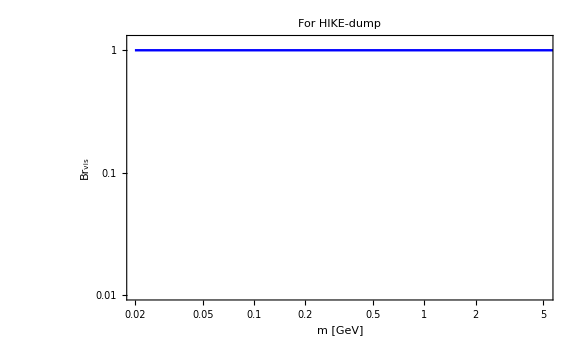

{1.75521,Null}

InterpolatingFunction[…](θa,za)

{1.7989,Null}

{1.21401,Null}

{1.23864,Null}

Search for ALPs coupled to photons at HIKE-dump located at SPS. N_collisions = 5.×10^19

Quantity | θ_min, rad | θ_max, rad | θ_min(ϵ_dec), rad | θ_max(ϵ_dec), rad | z_min, m | z_max, m
Description | Min angle covered by experiment | Max angle covered by experiment | Min angle where ϵ_decay≠0 | Max angle where ϵ_decay≠0 | Min long. displacement of the decay volume | Max long. displacement of the decay volume
Value | 0.00001 | 0.0126561 | 0.00001 | 0.0126561 | 78.93 | 183.93

```mathematica
SelectedExperiment=SelectedExperimentList[[icounter++]];
dataAcceptances=Import[FileNameJoin[{FileNameJoin[{NotebookDirectory[],"Acceptances",SelectedExperiment,ToString@StringForm["Acceptance_``_for_ALP-photon.m",SelectedExperiment]}]}],"MX"];//AbsoluteTiming
FacilityGivenExperiment=dataAcceptances[[1]];
ECALoption=dataAcceptances[[2]];
FullAcceptanceData0=dataAcceptances[[3]];
BrVisTemp[mFIP_]=dataAcceptances[[5]];
mlistBr=Join[Table[m,{m,0.02,5.1,0.005}]];
BrVis[mFIP_]=Interpolation[Table[{mFIP,BrVisTemp[mFIP]},{mFIP,mlistBr}],InterpolationOrder->1][mFIP];//AbsoluteTiming
LogLogPlot[BrVis[mFIP],{mFIP,0.02,10},Frame->True,ImageSize->Large,FrameStyle->Directive[Black, 22],PlotStyle->{{Thickness[0.003],Blue},{Thickness[0.003],Darker@Red},{Thickness[0.003],Darker@Darker@Green},{Thickness[0.003],Black}},GridLines->Automatic,PlotRange->{MinMax[mlistBr],{0.01,1.2}},Frame->True,ImageSize->Large,FrameLabel->{"m [GeV]","Br_vis"},PlotLabel-> Style[Row[{"For ",SelectedExperiment}], 20, Black]]
{θminExpAll,θmaxExpAll}=MinMax[FullAcceptanceData0[[All,2]]];
{θminExp,θmaxExp}=MinMax[Select[FullAcceptanceData0,#[[6]]≠0&][[All,2]]];
{zminExp,zmaxExp}=MinMax[FullAcceptanceData0[[All,4]]];
AzimuthalAcceptanceData=DeleteDuplicatesBy[FullAcceptanceData0,{#[[2]],#[[4]]}&][[All,{2,4,5}]];//AbsoluteTiming
θGrid=DeleteDuplicates[AzimuthalAcceptanceData[[All,1]]];
zminmaxθdata=Table[MinMax[Select[AzimuthalAcceptanceData,#[[1]]==θGrid[[i]]&&#[[3]]≠0&][[All,2]]],{i,1,Length[θGrid],1}];
zminθ[θa_]=Interpolation[Join[Partition[θGrid,1],zminmaxθdata[[All,{1}]],2],InterpolationOrder->1][θa];
zmaxθ[θa_]=Interpolation[Join[Partition[θGrid,1],zminmaxθdata[[All,{2}]],2],InterpolationOrder->1][θa];
AzimuthalAcceptanceALPphoton[θa_,za_]=Interpolation[{#[[1]],#[[2]],#[[3]]}&/@AzimuthalAcceptanceData,InterpolationOrder->1][θa,za]
DecAccDataLogarithmizedComp=Hold@Compile[{{FullAcceptanceData,_Real,2}},{Log10[#[[1]]],Log10[#[[2]]],Log10[#[[3]]],Log10[#[[4]]],Log10[#[[6]]]}&/@FullAcceptanceData]//ReleaseHold;
DecayAcceptanceALPphoton[ma_,θa_,Ea_,za_]=BrVis[ma]*10^(Interpolation[DecAccDataLogarithmizedComp[FullAcceptanceData0],InterpolationOrder->1][Log10[ma],Log10[θa],Log10[Ea],Log10[za]]);//AbsoluteTiming
(*Interpolation for the full acceptance*)
acccomp=Hold@Compile[{{data,_Real,2}},{Log10[#[[1]]],Log10[#[[2]]],Log10[#[[3]]],Log10[#[[4]]],If[#[[5]]*#[[6]]==0,-90,Log10[#[[5]]*#[[6]]]]}&/@SortBy[data,{#[[1]],#[[2]],#[[3]],#[[4]]}&]]//ReleaseHold;
(*Interpolation for the full acceptance*)
FullAcceptanceData=acccomp[FullAcceptanceData0];//AbsoluteTiming
FullAcceptanceALPphoton[ma_,θa_,Ea_,za_]=10^(Interpolation[FullAcceptanceData,InterpolationOrder->1][Log10[ma],Log10[θa],Log10[Ea],Log10[za]]);//AbsoluteTiming
CrossSectionData=dataAcceptances[[4]]//Transpose;
NpotGivenExperiment=Select[CrossSectionData,#[[1]]=="Npot"&][[1]][[2]]//N;
χprod["π^0"]=Select[CrossSectionData,#[[1]]=="PPi0"&][[1]][[2]];
χprod["η"]=Select[CrossSectionData,#[[1]]=="PEta"&][[1]][[2]];
(*infoDialog[Row[{"The number of proton collisions is ", NpotGivenExperiment,". You may change it at the stage of computing the sensitivities"}]]*)
Row[{"Search for ALPs coupled to photons at ", SelectedExperiment, " located at ",FacilityGivenExperiment,". N_collisions = ",NpotGivenExperiment}]
{{"Quantity","θ_min, rad","θ_max, rad","θ_min(ϵ_dec), rad","θ_max(ϵ_dec), rad","z_min, m","z_max, m"},{"Description","Min angle covered by experiment","Max angle covered by experiment","Min angle where ϵ_decay≠0","Max angle where ϵ_decay≠0","Min long. displacement of the decay volume","Max long. displacement of the decay volume"},{"Value",θminExpAll,θmaxExpAll,θminExp,θmaxExp,zminExp,zmaxExp}}//TableForm
```

## Angle-energy distributions for the given experiment

## ALP distributions

```mathematica
(*Fixing the target for Primakov and p-target production channels*)
DistrDirectory=FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/ALPs with photon coupling"}];
AvailableDistrPrimakovList=FileNames[ToString@StringForm["DoubleDistr-ALPs-from-Primakov-``-*",Sequence@@{FacilityGivenExperiment}],DistrDirectory];
AvailableDistrpCoherentList=FileNames[ToString@StringForm["DoubleDistr-ALPs-from-pCoherent-``-*",Sequence@@{FacilityGivenExperiment}],DistrDirectory];
TargetPrimakovDistr[i_]:=StringCases[Last@FileNameSplit@AvailableDistrPrimakovList[[i]],ToString@StringForm["DoubleDistr-ALPs-from-Primakov-``-target-",Sequence@@{FacilityGivenExperiment}]~~target__~~".dat":>{target}][[1]][[1]]
AvailableTargetsPrimakov=If[FacilityGivenExperiment=="SPS"||FacilityGivenExperiment=="FermilabBD"||SelectedExperiment=="FASER"||SelectedExperiment=="FASER2",Table[TargetPrimakovDistr[i],{i,1,Length[AvailableDistrPrimakovList],1}]];
TargetpCoherentDistr[i_]:=StringCases[Last@FileNameSplit@AvailableDistrpCoherentList[[i]],ToString@StringForm["DoubleDistr-ALPs-from-pCoherent-``-target-",Sequence@@{FacilityGivenExperiment}]~~target__~~".dat":>{target}][[1]][[1]]
AvailableTargetspCoherent=Table[TargetpCoherentDistr[i],{i,1,Length[AvailableDistrpCoherentList],1}];
Print["Selected target for the coherent Primakov production (works for experiments @ SPS, FermilabBD, and for FASER/FASER2:"]
TargetSelectedPrimakov=If[(FacilityGivenExperiment=="SPS"||FacilityGivenExperiment=="FermilabBD"),ChoiceDialog["Choose the target corresponding to the experiment (Primakov production):",AvailableTargetsPrimakov,Appearance->"Vertical"->{Automatic,3}],If[SelectedExperiment=="FASER"||SelectedExperiment=="FASER2",AvailableTargetsPrimakov[[1]]]]
Print["Selected target for the coherent p-target production:"]
TargetSelectedpCoherent=If[FacilityGivenExperiment=="SPS"||FacilityGivenExperiment=="FermilabBD",TargetSelectedPrimakov,"p"]
ALPDistributionFileNamesGivenExp=Join[{ToString@StringForm["DoubleDistr-ALPs-from-pCoherent-``-target-``.dat",Sequence@@{FacilityGivenExperiment,TargetSelectedpCoherent}],ToString@StringForm["DoubleDistr-ALPs-From-pi0-``.dat",Sequence@@{FacilityGivenExperiment}],ToString@StringForm["DoubleDistr-ALPs-From-Eta-``.dat",Sequence@@{FacilityGivenExperiment}]},If[FacilityGivenExperiment=="SPS"||FacilityGivenExperiment=="FermilabBD"||SelectedExperiment=="FASER"||SelectedExperiment=="FASER2",{ToString@StringForm["DoubleDistr-ALPs-from-Primakov-``-target-``.dat",Sequence@@{FacilityGivenExperiment,TargetSelectedPrimakov}]},{}]];
Do[If[!TrueQ@FileExistsQ@FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/ALPs with photon coupling/",ALPDistributionFileNamesGivenExp[[j]]}],Print[ALPDistributionFileNamesGivenExp[[j]]," does not exist. Generate it using module 2!"]
],{j,1,Length[ALPDistributionFileNamesGivenExp],1}]
Print["Production channels list:"]
ProductionList=Join[{"pCoherent","π^0","η"},If[FacilityGivenExperiment=="SPS"||FacilityGivenExperiment=="FermilabBD"||SelectedExperiment=="FASER"||SelectedExperiment=="FASER2",{"Primakov"},{}]]
ListExport:=Association[{"pCoherent"-> "pCoherent","π^0"->"Pi0","η"->"Eta","Primakov"->"Primakov"}]
Clear[j]
```

### Importing distributions and production probabilities

```mathematica
dataDistr[filename_]:=Import[FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/ALPs with photon coupling/",filename}],"Table"]
Do[
DataDistrALPphoton[ProductionList[[i]]]=dataDistr[ALPDistributionFileNamesGivenExp[[i]]]//N;
DoubleDistrALPphoton[ma_,θa_,Ea_,ProductionList[[i]]]=10^(Interpolation[{Log10[#[[1]]],Log10[#[[2]]],Log10[#[[3]]],Log10[#[[4]]+10^-90]}&/@DataDistrALPphoton[ProductionList[[i]]],InterpolationOrder->1][Log10[ma],Log10[θa],Log10[Ea]]);
mlistALPphoton[ProductionList[[i]]]=DeleteDuplicates[DataDistrALPphoton[ProductionList[[i]]][[All,1]]];
{mamin[ProductionList[[i]]],mamax[ProductionList[[i]]]}=MinMax[mlistALPphoton[ProductionList[[i]]]],{i,1,Length[ProductionList],1}]
χXtimesχXtoALPphoton[ma_,ga_,"Primakov"]=If[FacilityGivenExperiment=="SPS"||FacilityGivenExperiment=="FermilabBD"||SelectedExperiment=="FASER"||SelectedExperiment=="FASER2",ga^2*10^Interpolation[{Log10[#[[1]]],Log10[#[[2]]]}&/@Import[FileNameJoin[{NotebookDirectory[],"phenomenology/ALPs with photon coupling/branching ratios/",ToString@StringForm["Pprod-ALPs-from-Primakov-``-target-``.dat",Sequence@@{FacilityGivenExperiment,TargetSelectedPrimakov}]}],"Table"],InterpolationOrder->1][Log10[ma]],0];
χXtimesχXtoALPphoton[ma_,ga_,"pCoherent"]=ga^2*10^Interpolation[{Log10[#[[1]]],Log10[#[[2]]]}&/@Import[FileNameJoin[{NotebookDirectory[],"phenomenology/ALPs with photon coupling/branching ratios/",ToString@StringForm["Pprod-ALPs-from-pCoherent-``-target-``.dat",Sequence@@{FacilityGivenExperiment,TargetSelectedpCoherent}]}],"Table"],InterpolationOrder->1][Log10[ma]];
χXtimesχXtoALPphoton[ma_,ga_,"π^0"]=ga^2*χprod["π^0"]*Brπ0ToALP[ma];
χXtimesχXtoALPphoton[ma_,ga_,"η"]=ga^2*χprod["η"]*BrηToALP[ma];
LogLogPlot[Evaluate[Table[If[ma<Max[mlistALPphoton[ProductionList[[i]]]],Evaluate[χXtimesχXtoALPphoton[ma,1,ProductionList[[i]]]],0],{i,1,Length[ProductionList],1}]],{ma,0.02,1.5},Frame->True,ImageSize->Large,PlotRange->{All,{10^-6,10}},PlotLegends->Placed[Style[#,15]&/@ProductionList,Right]]
Export[FileNameJoin[{NotebookDirectory[],"Auxiliary data/ALPs with photon coupling",SelectedExperiment,"Double-Distr-Averaged-ALP-photon.m"}],{Sum[If[mamin[prod]<ma<mamax[prod],Evaluate[χXtimesχXtoALPphoton[ma,1,prod]],0],{prod,ProductionList}],1/Sum[If[mamin[prod]<ma<mamax[prod],Evaluate[χXtimesχXtoALPphoton[ma,1,prod]],0],{prod,ProductionList}] Sum[If[mamin[prod]<ma<mamax[prod],Evaluate[χXtimesχXtoALPphoton[ma,1,prod]*DoubleDistrALPphoton[ma,θa,Ea,prod]],0],{prod,ProductionList}]},"MX"]
```

### Determining min/max energies of scalars for the given polar angle. Needed for stability of Monte-Carlo integration

#### Common definition

```mathematica
EfromXmax[mass_,data_,LogMin_]:=Module[{distr},
datt=Select[data,#[[1]]==mass&];
EmaxVal=datt[[All,3]]//Max;
θlist=Table[x,{x,θminExp,θmaxExp,(θmaxExp-θminExp)/5}];
distr[θfip_,Efip_]=Abs[Evaluate[Interpolation[{#[[2]],#[[3]],#[[4]]+10^-90}&/@datt,InterpolationOrder->1][θfip,Efip]]];
DoubleDistrIntList[i_]:=Interpolation[ParallelTable[{Efip,Quiet[NIntegrate[distr[θfip,Efip],{θfip,θlist[[i]],θlist[[i+1]]},Method->"AdaptiveMonteCarlo"]]},{Efip,Table[10^x,{x,Log10[1.1*mass],Log10[EmaxVal],(Log10[EmaxVal]-Log10[1.1*mass])/50.}]}],InterpolationOrder->1][Efip];
θfipdistrlist[Efip_]=Table[{(θlist[[i]]+θlist[[i+1]])/2,DoubleDistrIntList[i]},{i,1,Length[θlist]-1,1}];
θEmaxList=Table[{θfipdistrlist[Efip][[i]][[1]],SortBy[Table[{Efip,θfipdistrlist[Efip][[i]][[2]]},{Efip,mass,EmaxVal,1}],-#[[2]]&][[1]][[1]]},{i,1,Length[θfipdistrlist[Efip]],1}];
θEmaxListInt[θfip_]=Interpolation[θEmaxList,InterpolationOrder->1][θfip];
NormVals=Table[NIntegrate[θfipdistrlist[Efip][[i]][[2]]+10^-90.,{Efip,mass,EmaxVal},Method->"InterpolationPointsSubdivision"],{i,1,Length[θfipdistrlist[Efip]],1}];
cdf[es_,i_]:=1-1/NormVals[[i]] NIntegrate[θfipdistrlist[Efip][[i]][[2]],{Efip,mass,es},Method->"InterpolationPointsSubdivision"];
cdftab[Efip_]=Table[{θfipdistrlist[Efip][[i]][[1]],Interpolation[ParallelTable[{10^es,Quiet[cdf[10^es,i]]},{es,Log10[mass],Log10[EmaxVal],(Log10[EmaxVal]-Log10[mass])/50}],InterpolationOrder->1][Efip]},{i,1,Length[θfipdistrlist[Efip]],1}];
logmin[θfip_]=LogMin;
Estart[θfip_]=Min[2*θEmaxListInt[θfip],0.9*EmaxVal];
Emaxv[i_]:=If[NormVals[[i]]<10^-15,mass,10^(Efip/.FindRoot[Log10[cdftab[10^Efip][[i]][[2]]]==logmin[θEmaxList[[i]][[1]]],{Efip,Log10[Estart[θEmaxList[[i]][[1]]]],Log10[θEmaxList[[i]][[2]]],Log10[EmaxVal]}])];
tabtemp=Table[{θEmaxList[[i]][[1]],Emaxv[i]},{i,1,Length[θEmaxList],1}];
tab=Join[{{θminExp,tabtemp[[1]][[2]]}},Drop[Drop[tabtemp,1],-1],{{θmaxExp,tabtemp[[-1]][[2]]}}];
10^(Interpolation[{Log10[#[[1]]],Log10[#[[2]]]}&/@tab,InterpolationOrder->1][Log10[θfip]])
]
EmaxBlock[data_,logmin_]:=Module[{mlist},
mlist=Drop[data[[All,1]],-1];
EmaxTemp[m_,θ_]=Max[m,EfromXmax[mlist[[1]],data,logmin],EfromXmax[mlist[[-1]],data,logmin]]/.{θfip->θ};
θlist=Table[x,{x,θminExp,θmaxExp,(θmaxExp-θminExp)/10}];
10^(Interpolation[{#[[1]],Log10[#[[2]]],Log10[#[[3]]]}&/@Flatten[Table[{mfip,θfip,EmaxTemp[mfip,θfip]},{mfip,mlist[[1]],mlist[[-1]],(mlist[[-1]]-mlist[[1]])/10},{θfip,θlist}],{1,2}],InterpolationOrder->1][mfip,Log10[θfip]])
]
Do[Eamax[mfip_,θfip_,prod]=EmaxBlock[DataDistrALPphoton[prod],-5],{prod,ProductionList}]//AbsoluteTiming
{EminALPphotonForPlot,EamaxForPlot}=MinMax[Table[Eamax[ma,θa,prod],{prod,ProductionList},{θa,{θminExp,θmaxExp}},{ma,MinMax[mlistALPphoton[prod]]}]];
LogLogPlot[Evaluate[Table[Eamax[0.05,θa,prod],{prod,ProductionList}]],{θa,θminExp,θmaxExp},ImageSize->Large,Frame->True,PlotRange->{All,{0.8*EminALPphotonForPlot,1.2*EamaxForPlot}},PlotLegends->Placed[Style[#,15]&/@ProductionList,Right]]
```

## Number of events

## Definitions

### Grids for the initial data with acceptances and distributions

```mathematica
(*Grid Subscript[m, S], Subscript[θ, S], Subscript[E, S], Subscript[z, S] for the initial acceptance data, logarithmized*)
InGridmϵ=DeleteDuplicates[FullAcceptanceData[[All,1]]];
InGridθϵ=DeleteDuplicates[FullAcceptanceData[[All,2]]];
InGridEϵ=DeleteDuplicates[FullAcceptanceData[[All,3]]];
InGridzϵ=DeleteDuplicates[FullAcceptanceData[[All,4]]];
(*Array of values of the initial acceptance data, reshaped*)
ϵvals=ArrayReshape[FullAcceptanceData[[All,5]],{Length[InGridmϵ],Length[InGridθϵ],Length[InGridEϵ],Length[InGridzϵ]}];
ϵazValscomp=Compile[{{data,_Real,2}},Table[If[data[[i]][[5]]==0,-90.,Log10[data[[i]][[5]]]],{i,1,Length[data],1}],CompilationTarget->"C",RuntimeOptions->"Speed"];
ϵazvals=ArrayReshape[ϵazValscomp[FullAcceptanceData0],{Length[InGridmϵ],Length[InGridθϵ],Length[InGridEϵ],Length[InGridzϵ]}];
(*_________________________________________________________________*)
(*Grid Subscript[m, S], Subscript[θ, S], Subscript[E, S] for the initial FIP distribution data, logarithmized*)
DataLogarithmiedComp=Hold@Compile[{{data,_Real,2}},Table[If[data[[i]][[4]]==0,-90.,Log10[data[[i]][[4]]]],{i,1,Length[data],1}],CompilationTarget->"C",RuntimeOptions->"Speed"]//ReleaseHold
BlockGridsValsDistr[ProdChannel_]:=Module[{GridIn,vals},
GridIn=Log10[DeleteDuplicates[DataDistrALPphoton[ProdChannel][[All,#]]]&/@{1,2,3}];
vals=ArrayReshape[DataLogarithmiedComp[DataDistrALPphoton[ProdChannel]],{Length[GridIn[[1]]],Length[GridIn[[2]]],Length[GridIn[[3]]]}];
{GridIn,vals}
]
Do[{GridInFinal[prod],DistrVals[prod]}=BlockGridsValsDistr[prod],{prod,ProductionList}];//AbsoluteTiming
```

### Grid to be used to calculate the number of events

```mathematica
(*Grid Subscript[θ, S], Subscript[z, S] for the final acceptance data, logarithmized*)
OutGridθfinal=(*InGridθϵ*)Log10[Table[x,{x,10^Min[InGridθϵ],10^Max[InGridθϵ],(10^Max[InGridθϵ]-10^Min[InGridθϵ])/30}]];
OutGridzfinal=Log10[Table[x,{x,10^InGridzϵ[[1]],10^InGridzϵ[[-1]],Min[(10^InGridzϵ[[-1]]-10^InGridzϵ[[1]])/5,Max[0.5,(10^InGridzϵ[[-1]]-10^InGridzϵ[[1]])/30]]}]](*InGridzϵ*);
ΔxVals[list_]:=Join[{(list[[2]]-list[[1]])/2},Table[list[[i]]-list[[i-1]],{i,2,Length[list],1}]];
Δθvals=ΔxVals[10^OutGridθfinal];
Δzvals=ΔxVals[10^OutGridzfinal];
(*Final energy grid. Mass- and production channel-dependent*)
StepEtemp[Efip_]=Piecewise[{{0.3,Efip≤2.5},{0.5,2.5<Efip<35},{2,35≤Efip≤50},{4,50<Efip<160},{5,160≤Efip<300},{40,300≤Efip<700},{50,700≤Efip<2000},{200,2000≤Efip<4000},{400,4000≤Efip<7000},{500,7000≤Efip≤50000}}];
OutGridEnergy[m_,ProdChannel_]:=Block[{},
With[{start=1.01m,end=Eamax[m,θminExp,ProdChannel]},
Log10[NestWhileList[#+StepEtemp[#]&,start,#≤end&,1,∞,-1]]]//N
]
ΔxValsTotComp=Hold@Compile[{{Δθvals,_Real,1},{ΔEvals,_Real,1},{Δzvals,_Real,1}},Table[{Δθvals[[i]]*ΔEvals[[j]]*Δzvals[[k]]},{i,1,Length[Δθvals]},{j,1,Length[ΔEvals]},{k,1,Length[Δzvals]}],CompilationTarget->"C",RuntimeOptions->"Speed"]//ReleaseHold;
```

### Code that computes the number of events - using the mapping method

#### Grid for distribution times acceptance

```mathematica
(*Block that computes the grid Subscript[θ, S],Subscript[E, S],Subscript[z, S], Subscript[ϵ, Full]×Subscript[f, Subscript[θ, S],Subscript[E, S]]*)
TableIntegrandDiscret[m_,ProdChannel_,ϵDecOp_]:=Block[{},
OutGridEfinal=OutGridEnergy[N[m],ProdChannel];
ΔEvals=ΔxVals[10^OutGridEfinal];
ΔxValsTot=Flatten[ΔxValsTotComp[Δθvals,ΔEvals,Δzvals],{1,2,3}];
OutGridFinal=Tuples[{{Log10[N[m]]},OutGridθfinal,OutGridEfinal,OutGridzfinal}];
OutGridFinal1=10^OutGridFinal[[All,{2,3,4}]];
gϵ={InGridmϵ,InGridθϵ,InGridEϵ,InGridzϵ};
xgϵ={{Log10[N[m]]},OutGridθfinal,OutGridEfinal,OutGridzfinal};
xigϵ=MapThread[Interpolation[Transpose@{#,Range@Length@#},InterpolationOrder->1][#2]&,{gϵ,xgϵ}];
ϵResult=10^Flatten@cf4[Sequence@@xigϵ,If[ϵDecOp=="True",ϵvals,ϵazvals]];
gDistr={GridInFinal[ProdChannel][[1]],GridInFinal[ProdChannel][[2]],GridInFinal[ProdChannel][[3]]};
xgDistr={{Log10[N[m]]},OutGridθfinal,OutGridEfinal};
xigDistr=MapThread[Interpolation[Transpose@{#,Range@Length@#},InterpolationOrder->1][#2]&,{gDistr,xgDistr}];
DistrResult=10^Flatten@cf3[Sequence@@xigDistr,DistrVals[ProdChannel]];
TabTemp0=Join[OutGridFinal1,List/@Flatten[DistrResult Partition[ϵResult,Length[OutGridzfinal]]],ΔxValsTot,2]
]
```

#### Convoluting acceptances with pre-factor

```mathematica
(*Values Subscript[f, FIP]×Subscript[ϵ, FIP]×Exp[-Subscript[z, FIP]/(cos(Subscript[θ, FIP])Subscript[cτ, FIP] Subscript[p, FIP]/Subscript[m, FIP])]/(cos(Subscript[θ, FIP])Subscript[cτ, FIP] Subscript[p, FIP]/Subscript[m, FIP])×Subscript[ϵ, decay] Subscript[Δz, FIP] Subscript[ΔE, FIP] Subscript[Δθ, FIP] for the grid of values Subscript[θ, FIP], Subscript[E, FIP], Subscript[z, FIP] fixed values of Subscript[cτ, FIP] and Subscript[m, FIP]*)
tableprefac=Hold@Compile[{{tabb,_Real,1},{m,_Real},{cτ,_Real},{decProb,_Integer},{zshift,_Real}},Module[{angles,energies,zv,values,Δs,prefactor},
values=Compile`GetElement[tabb,4];
Δs=Compile`GetElement[tabb,5];
If[decProb==1,
angles=Compile`GetElement[tabb,1];
energies=Compile`GetElement[tabb,2];
zv=Compile`GetElement[tabb,3];
prefactor=Exp[-(zv-zshift)/(Cos[angles]*cτ*(√(energies^2-m^2))/m)]/(Cos[angles]*cτ*(√(energies^2-m^2))/m),prefactor=1.];
prefactor*Δs*values],CompilationTarget->"C",RuntimeOptions->"Speed",Parallelization->"True",RuntimeAttributes->{Listable}]//ReleaseHold;
(*Summation of the values above*)
sumcompile=Hold@Compile[{{tabcτm,_Real,1}},Total[tabcτm],CompilationTarget->"C",RuntimeOptions->"Speed",Parallelization->"True"]//ReleaseHold;
{mminϵ,mmaxϵ}=10^MinMax[InGridmϵ]
```

#### Acceptances

```mathematica
FactorANUBISceiling=If[SelectedExperiment=="ANUBIS-ceiling",2,1];
AcceptanceDiscret[m_,ProdChannel_,ϵdecOp_,decProb_,zshift_]:=Module[{NevDiscret,NpotTimesχval},
If[Max[mamin[ProdChannel],mminϵ]<m<Min[mamax[ProdChannel],mmaxϵ],
integrandtab=TableIntegrandDiscret[m,ProdChannel,ϵdecOp];
brvis=If[ϵdecOp==1,BrVis[m],1];
(*Test lifetime for the acceptance*)
cτacc=10^9;
(*Prefactor for the acceptance. If only azimuthal and *)
prefacacc=If[decProb==1,cτacc,1/(zmaxExp-zminExp)];
accdiscret=If[brvis!=0,FactorANUBISceiling*brvis*prefacacc*sumcompile[tableprefac[integrandtab,m,cτacc,decProb,zshift]],0],accdiscret=0];
accdiscret
]
```

## Acceptances and approximate lower/upper bounds computation

```mathematica
zMinShift[prod_]:=If[prod=="Primakov"&&(SelectedExperiment=="FASER"||SelectedExperiment=="FASER2"),130.,0.]
Do[zshiftval[prod]=zMinShift[prod],{prod,ProductionList}];
Do[mlistAcceptance[prod]=Join[Table[m,{m,1.01Max[mamin[prod],mminϵ],0.95Min[mamax[prod],mmaxϵ],Min[(0.95Min[mamax[prod],mmaxϵ]-1.01Max[mamin[prod],mminϵ])/20,2]}],{0.99Min[mamax[prod],mmaxϵ]}],{prod,ProductionList}];
Do[ϵGeomTabs[prod]=Table[{m,AcceptanceDiscret[m,prod,"False",0,zshiftval[prod]],AcceptanceDiscret[m,prod,"True",0,zshiftval[prod]],AcceptanceDiscret[m,prod,"False",1,zshiftval[prod]],AcceptanceDiscret[m,prod,"True",1,zshiftval[prod]]},{m,mlistAcceptance[prod]}],{prod,ProductionList}];//AbsoluteTiming
PlotAcc[ProdChannel_]:=ListLogPlot[{ϵGeomTabs[ProdChannel][[All,{1,2}]],ϵGeomTabs[ProdChannel][[All,{1,3}]],ϵGeomTabs[ProdChannel][[All,{1,4}]],ϵGeomTabs[ProdChannel][[All,{1,5}]]},FrameStyle->Directive[Black, 22],PlotStyle->{{Thickness[0.003],Blue},{Thickness[0.003],Darker@Red},{Thickness[0.003],Darker@Darker@Green},{Thickness[0.003],Black}},GridLines->Automatic,PlotRange->{MinMax[ϵGeomTabs[ProdChannel][[All,1]]],{0.9Min[Min[ϵGeomTabs[ProdChannel][[All,4]]],Min[ϵGeomTabs[ProdChannel][[All,3]]]],1.1Max[Max[ϵGeomTabs[ProdChannel][[All,2]]],Max[ϵGeomTabs[ProdChannel][[All,4]]]]}},Joined->True,Frame->True,ImageSize->Large,FrameLabel->{"m [GeV]","Acceptance"},PlotLabel-> Style[Row[{"From ",ProdChannel}], 20, Black],PlotLegends->Placed[{Style[#, 18]&/@{"<ϵ_FIP>","<ϵ_FIPϵ_decay>","cτ<ϵ_FIPP_decay>","cτ<ϵ_FIPP_decayϵ_decay>"}},{0.75,0.2}]]
Style[Row[Evaluate[Table[PlotAcc[prod],{prod,ProductionList}]]],ImageSizeMultipliers->{1,1,1,1}]
(*Do[FilenameAcceptance[prod]=ToString@StringForm["Acceptance_ALP-photon_at_``_From_``.dat",Sequence@@{SelectedExperiment,ListExport[prod]}];
Export[FileNameJoin[{NotebookDirectory[],"Auxiliary data/ALPs with photon coupling",SelectedExperiment,FilenameAcceptance[prod]}],ϵGeomTabs[prod][[All,{1,2,4,5}]],"Table"]
,{prod,ProductionList}]*)
AccAveraged[ma_]=NpotGivenExperiment*{Sum[If[mamin[prod]<ma<mamax[prod],Evaluate[χXtimesχXtoALPphoton[ma,1,prod]],0],{prod,ProductionList}],Sum[If[Max[mamin[prod],mminϵ]<ma<Min[mamax[prod],mmaxϵ],Evaluate[χXtimesχXtoALPphoton[ma,1,prod]*Interpolation[ϵGeomTabs[prod][[All,{1,2}]],InterpolationOrder->1][ma]],0],{prod,ProductionList}],Sum[If[Max[mamin[prod],mminϵ]<ma<Min[mamax[prod],mmaxϵ],Evaluate[χXtimesχXtoALPphoton[ma,1,prod]/cτacc*Interpolation[ϵGeomTabs[prod][[All,{1,4}]],InterpolationOrder->1][ma]],0],{prod,ProductionList}],Sum[If[Max[mamin[prod],mminϵ]<ma<Min[mamax[prod],mmaxϵ],Evaluate[χXtimesχXtoALPphoton[ma,1,prod]/cτacc*Interpolation[ϵGeomTabs[prod][[All,{1,5}]],InterpolationOrder->1][ma]],0],{prod,ProductionList}]};
Export[FileNameJoin[{NotebookDirectory[],"Auxiliary data/ALPs with photon coupling",SelectedExperiment,"AcceptanceAveragedALPphoton.m"}],AccAveraged[ma],"MX"]
```

### Rough estimates of the upper and lower bounds

#### Definitions

```mathematica
Do[gaminEstimate[ma_,prod]=((NpotGivenExperiment*χXtimesχXtoALPphoton[ma,1,prod]*Interpolation[ϵGeomTabs[prod][[All,{1,5}]],InterpolationOrder->1][ma])/(2.3ldecayALPphoton[ma,1,Ea]*ma/(√(Ea^2-ma^2))))^(-1/4.);
gamaxEstimate[ma_,prod]=Re[(Re[Evaluate[-ProductLog[-1,-2.3*b/a]/b/.{a-> NpotGivenExperiment*χXtimesχXtoALPphoton[ma,1,prod]*Interpolation[ϵGeomTabs[prod][[All,{1,3}]],InterpolationOrder->1][ma],b->(zminExp-zshiftval[prod])/ldecayALPphoton[ma,1,Eamax[mlistALPphoton[prod][[1]],θminExp,prod]]}]])^(1/2.)],{prod,ProductionList}]
ϵestplot="η";
LogLogPlot[{gaminEstimate[ma,ϵestplot],gamaxEstimate[ma,ϵestplot]},{ma,Min[mlistALPphoton[ϵestplot]],Max[mlistALPphoton[ϵestplot]]},Frame->True,ImageSize->Large]
```

## Number of events

### Number of events - fast

```mathematica
FactorLowerBound=If[MemberQ[{"ANUBIS-shaft-volume-1","ANUBIS-shaft-volume-2","ANUBIS-shaft-volume-3"},SelectedExperiment]==True,0.1,0.3];
NeventsDiscret[m_,ProdChannel_,galist_]:=Module[{NevDiscret,NpotTimesχval,zshift},
If[Max[mamin[ProdChannel],mminϵ]<m<Min[mamax[ProdChannel],mmaxϵ],
integrandtab=TableIntegrandDiscret[m,ProdChannel,"True"];
NpotTimesχval[ga_]=NpotGivenExperiment*χXtimesχXtoALPphoton[m,ga,ProdChannel];
{lowerbound,upperbound}={gaminEstimate[m,ProdChannel],gamaxEstimate[m,ProdChannel]};
brvis=BrVis[m];
zshift=zMinShift[ProdChannel];
NevDiscret[ga_]:=If[0.1lowerbound<ga<(*1.5*)2upperbound,NpotTimesχval[ga]*brvis*sumcompile[tableprefac[integrandtab,m,cτALPphoton[m,ga],1,zshift]],0];
Table[{m,galist[[i]],NevDiscret[galist[[i]]]},{i,1,Length[galist],1}],Table[{m,galist[[i]],0},{i,1,Length[galist],1}]]
]
```

### Number of events - slow (using built-in Mathematica functions Interpolation, NIntegrate)

```mathematica
(*Differential decay probability 1/ldecay Exp[-l/ldecay], where l is expressed in terms of the longitudinal displacement z and polar angle θ as z/cosθ*)
PdecayDensity[ma_,ga_,θa_,Ea_,za_]=Exp[-za/(Cos[θa]*ldecayALPphoton[ma,ga,Ea])]/(Cos[θa]*ldecayALPphoton[ma,ga,Ea]);
(*The integrand determining the differential rate for events*)
Do[IntegrandALPphoton[ma_,ga_,θa_,Ea_,za_,prod]=DoubleDistrALPphoton[ma,θa,Ea,prod]*PdecayDensity[ma,ga,θa,Ea,za-zMinShift[prod]]*AzimuthalAcceptanceALPphoton[θa,za]*Min[DecayAcceptanceALPphoton[ma,θa,Ea,za],1],{prod,ProductionList}];
IntegralALPphoton[ma_,ga_,ProdChannel_]:=NIntegrate[Abs[IntegrandALPphoton[ma,ga,θa,Ea,z,ProdChannel]],{θa,θminExp,θmaxExp},{Ea,ma,Eamax[ma,θa,ProdChannel]},{z,zminθ[θa],zmaxθ[θa]},Method->"AdaptiveMonteCarlo"]
Nevents[ma_,ga_,ProdChannel_]:=If[mamin[ProdChannel]≤ma≤mamax[ProdChannel],If[0.3*gaminEstimate[ma,ProdChannel]<ga<1.8gamaxEstimate[ma,ProdChannel],NpotGivenExperiment*χXtimesχXtoALPphoton[ma,ga,ProdChannel]*IntegralALPphoton[ma,ga,ProdChannel],0],0]
```

#### Test

```mathematica
(*This is a comparison between the slow and fast integration methods. For the selected mass and production channel, the numbers of events obtained using the methods should agree within 10%*)
(*If the agreement is worse, there may be a few reasons*)
(*1) The grid for the fast method is not dense enough. Try to increase the grid density (OutGridθfinal, OutGridEfinal, OutGridzfinal) to see whether the agreement improves. Sometimes, even a slightly denser grid for e.g. z may lead to a significant improvement in the agrement*)
(*2) The Monte-Carlo integrator for the slow method fails to evaluate properly; this may happen if the range of the integration over energies is too large compared to the domain where most of the events actually are (off-axis experiments such as MATHUSLA and ANUBIS). Another symptom is that for the given mass and coupling the integral "jumps", i.e., returns values with large error*)
mtest=2.7;
ProdTest="Primakov";
galist=(*{10^-12,3*10^-12,5*10^-12,10^-11,5*10^-11,10^-10,5*10^-10,10^-9,5*10^-9,10^-8,2*10^-8,4*10^-8,10^-7,5*10^-7,6*10^-7,7*10^-7,8*10^-7,9*10^-7,10^-6,2*10^-6}//N*)Table[10^x,{x,-12.,-2.,0.1}];
dat1=NeventsDiscret[mtest,ProdTest,galist];//AbsoluteTiming
dat2=ParallelTable[{galist[[i]],cτALPphoton[mtest,galist[[i]]],Nevents[mtest,galist[[i]],ProdTest]},{i,1,Length[galist],1}];//AbsoluteTiming
Join[dat1,dat2[[All,{3,2}]],2]//TableForm
```

### Differential number of events

```mathematica
(*The same as tableprefac but also including the grid*)
tableGridPrefac=Hold@Compile[{{tabb,_Real,2},{mS,_Real},{cτ,_Real},{zshift,_Real}},{#[[1]],#[[2]],#[[3]],Exp[-(#[[3]]-zshift)/(Cos[#[[1]]]*cτ*(√((#[[2]])^2-mS^2))/mS)]/(Cos[#[[1]]]*cτ*(√((#[[2]])^2-mS^2))/mS)#[[4]]*#[[5]]}&/@tabb,CompilationTarget->"C",RuntimeOptions->"Speed",Parallelization->"True",RuntimeAttributes->{Listable}]//ReleaseHold;
(*Summation returning the differential number of events X, df/dX *)
NdiffCompiled=Hold@Compile[{{tabNdiff,_Real,2},{GridQuantity,_Real,1},{LengthPerVariable,_Integer},{NPoTtimesPprod,_Real}},Table[{tabNdiff[[LengthPerVariable*(i-1)+1]][[1]],NPoTtimesPprod*Sum[tabNdiff[[LengthPerVariable*(i-1)+j]][[4]],{j,1,LengthPerVariable,1}]},{i,1,Length[GridQuantity],1}],CompilationTarget->"C",RuntimeOptions->"Speed",Parallelization->"True"]//ReleaseHold
(*Variable = "E_X","x_x","θ_X". The number belongs to the column in the tabulated data*)
iVal:=Association[{"E_X" ->2,"θ_X"->1,"x_x"->3}]
(*Differential number of events*)
NeventsDifferentialDiscret[m_,ProdChannel_,ga_,Variable_]:=Module[{NpotTimesχval},
ival=iVal[Variable];
NpotTimesχval=NpotGivenExperiment*χXtimesχXtoALPphoton[m,ga,ProdChannel];
tablegrid0=TableIntegrandDiscret[m,ProdChannel,"True"];
Δxvals:=Association[{"E_X"->ΔEvals,"θ_X"-> Δθvals,"x_X"-> Δzvals}];
Δxval=Δxvals[Variable];
cτVal=cτALPphoton[m,ga];
brvis=BrVis[m];
ilist=DeleteDuplicates[{ival,1,2,3}];
zshift=zMinShift[ProdChannel];
tablegrid1=SortBy[{#[[ilist[[1]]]],#[[ilist[[2]]]],#[[ilist[[3]]]],#[[4]]}&/@tableGridPrefac[tablegrid0,m,cτVal,zshift],{#[[1]],#[[2]],#[[3]]}&];
GridQuantity=tablegrid1[[All,1]]//DeleteDuplicates;
LengthPerVariable=Length[tablegrid1]/Length[GridQuantity];
tab1=NdiffCompiled[tablegrid1,GridQuantity,LengthPerVariable,NpotTimesχval*brvis];
Join[tab1[[All,{1}]],Partition[tab1[[All,2]]*Δxval^-1,1],2]
]
mvaltest=0.3;
gatest=10^-6;
quantity="E_X";
LegendX:=Association[{"E_X"->"E_a [GeV]","θ_X"->"θ_a [rad]","x_X"-> "z_a [m]"}]
LegendY:=Association[{"E_X"->"dN_ev/dE_a [GeV^-1]","θ_X"->"dN_ev/dθ_a [rad^-1]","x_X"-> "dN_ev/dz_a [m^-1]"}]
prodlisttemp={};
Do[If[Max[mamin[prod],mminϵ]<mvaltest<Min[mamax[prod],mmaxϵ],
prodlisttemp=Join[prodlisttemp,{prod}];
NdiffData[prod]=NeventsDifferentialDiscret[mvaltest,prod,gatest,quantity];
XvalminmaxNdiff=Select[NdiffData[prod],#[[2]]>10^-40&][[All,1]]//MinMax;
NdiffInt[X_,prod]=If[XvalminmaxNdiff[[1]]<X<XvalminmaxNdiff[[2]],Evaluate[10^Interpolation[{Log10[#[[1]]],Log10[#[[2]]+10^-90]}&/@NdiffData[prod],InterpolationOrder->1][Log10[X]]],0]],{prod,ProductionList}];
NdiffInt[X_,"Total"]=Sum[NdiffInt[X,prod],{prod,prodlisttemp}];
LegendList=Join[{"Total"},prodlisttemp];
QuantityMinMax=Flatten[Table[MinMax[NdiffData[prod][[All,1]]],{prod,prodlisttemp}],1]//MinMax
ValueMinMax=Max[Max[NdiffData[#][[All,2]]]&/@prodlisttemp];
LogLogPlot[Evaluate[Table[NdiffInt[X,prod],{prod,LegendList}]],{X,QuantityMinMax[[1]],QuantityMinMax[[2]]},Frame->True,ImageSize->Large,PlotRange->{All,{10^-5,2ValueMinMax}},PlotStyle->{{Thick,Black},{Thick,Blue},{Thick,Darker@Red},{Thick,Darker@Darker@Green},{Thick,Darker@Cyan},{Thick,Magenta},{Thick,Blue,Dashing[0.02]},{Thick,Darker@Red,Dashing[0.02]},{Thick,Darker@Darker@Green,Dashing[0.02]}},PlotLegends->Placed[Style[#,20]&/@LegendList,{0.85,0.7}],FrameLabel->{LegendX[quantity] ,LegendY[quantity]},FrameStyle->Directive[Black, 23],PlotLabel->Style[Row[{SelectedExperiment,". m_a = ", mvaltest," GeV, g_a = ", gatest//N," GeV^-1"}],20,Black]]
```

# Exporting tabulated number of events

## Definitions

```mathematica
If[(DirectoryQ[FileNameJoin[{NotebookDirectory[],"Tabulated Nevents"}]]//ToString)=="False",CreateDirectory[FileNameJoin[{NotebookDirectory[],"Tabulated Nevents"}]]];
If[(DirectoryQ[FileNameJoin[{NotebookDirectory[],"Tabulated Nevents/ALPs with photon coupling"}]]//ToString)=="False",CreateDirectory[FileNameJoin[{NotebookDirectory[],"Tabulated Nevents/ALPs with photon coupling"}]]];
If[(DirectoryQ[FileNameJoin[{NotebookDirectory[],"Tabulated Nevents/ALPs with photon coupling",SelectedExperiment}]]//ToString)=="False",CreateDirectory[FileNameJoin[{NotebookDirectory[],"Tabulated Nevents/ALPs with photon coupling",SelectedExperiment}]]];
Print["Filenames with tabulated N_events:"]
Do[FilenameNevents[prod]=ToString@StringForm["Nevents_ALP-photon_at_``_Npot=``_From_``.dat",Sequence@@{SelectedExperiment,NpotGivenExperiment//CForm//ToString,ListExport[prod]}],{prod,ProductionList}]
Table[FilenameNevents[prod],{prod,ProductionList}]//TableForm
MassListALPphotonExport={0.021,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.15,0.2,0.22,0.25,0.3,0.35,0.4,0.5,0.55,0.6,0.7,0.8,0.9,1,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.,2.1,2.2,2.3,2.4,2.5,2.6,2.7,2.8,2.9,3.,3.1,3.2,3.3,3.4,3.5}//N;
garange=Table[10^x,{x,-12,-2,0.02}];
```

## Exporting

## Common definition

```mathematica
BlockExport[ProdChannel_]:=Block[{},
If[Select[ProductionList,#==ProdChannel&]=={},,
masslist=MassListALPphotonExport;
TabFrom=Monitor[Table[NeventsDiscret[masslist[[k]],ProdChannel,garange],{k,1,Length[masslist],1}],Row[{ProgressIndicator[k,{1,Length[masslist]}],"i = ",k,"/",Length[masslist],", m = ",masslist[[k]]," GeV"}," "]];
Export[FileNameJoin[{NotebookDirectory[],"Tabulated Nevents/ALPs with photon coupling",SelectedExperiment,FilenameNevents[ProdChannel]}],Flatten[TabFrom,1],"Table"]]
]
```

## From pCoherent

```mathematica
BlockExport["pCoherent"];//AbsoluteTiming
```

## From Primakov

```mathematica
BlockExport["Primakov"];//AbsoluteTiming
```

## From π^0

```mathematica
BlockExport["π^0"];//AbsoluteTiming
```

## From η

```mathematica
BlockExport["η"];//AbsoluteTiming
```

# Computing sensitivities

## Specifying the experiment and interpolating the tabulated number of events

```mathematica
If[(DirectoryQ[FileNameJoin[{NotebookDirectory[],"Sensitivity domains"}]]//ToString)=="False",CreateDirectory[FileNameJoin[{NotebookDirectory[],"Sensitivity domains"}]]]
If[(DirectoryQ[FileNameJoin[{NotebookDirectory[],"Sensitivity domains","ALPs with photon coupling"}]]//ToString)=="False",CreateDirectory[FileNameJoin[{NotebookDirectory[],"Sensitivity domains","ALPs with photon coupling"}]]]
NeventsDirectory=FileNameJoin[{NotebookDirectory[],"Tabulated Nevents","ALPs with photon coupling"}];
ExperimentDirectoriesListNevents=Select[FileNames["*",NeventsDirectory,1],DirectoryQ];
Print["List of available experiments with tabulated N_events for ALPs with the coupling to photons:"]
ExperimentsListNevents=Table[FileNameTake[ExperimentDirectoriesListNevents[[i]],-1],{i,1,Length[ExperimentDirectoriesListNevents],1}]//Sort;
ExperimentsListNevents//TableForm
If[Length[ExperimentsListNevents]==0,Print["No experiment is available, generate first the acceptance for the given experiment using module 1"]]
Print["Selected experiment:"]
dropdownDialog[list_,phrase_]:=DialogInput[{choice=""},Column[{TextCell[phrase],PopupMenu[Dynamic[choice],list],Button["OK",DialogReturn[choice]]}]]
If[Length[ExperimentsListNevents]≠0,GivenExperimentForSensitivityComputation=dropdownDialog[ExperimentsListNevents,"Select the experiment:"]]
CondANUBIS=MemberQ[{"ANUBIS-shaft-volume-1","ANUBIS-shaft-volume-2","ANUBIS-shaft-volume-3"},GivenExperimentForSensitivityComputation];
If[CondANUBIS==True,infoDialog[Row[{"One of the modules of ANUBIS-shaft is chosen. The full sensitivity includes three modules. The importing will be over all modules, so for all ot the the sensitivity has to be computed"}]]]
If[CondANUBIS==False,GivenExperimentForSensitivityComputationList={GivenExperimentForSensitivityComputation},GivenExperimentForSensitivityComputationList={"ANUBIS-shaft-volume-1","ANUBIS-shaft-volume-2","ANUBIS-shaft-volume-3"}];
filesNevents={};
Do[filesNevents=Join[filesNevents,FileNames["*.dat",FileNameJoin[{NotebookDirectory[],"Tabulated Nevents/ALPs with photon coupling",exp}]]],{exp,GivenExperimentForSensitivityComputationList}];
Print["Production channels:"]
FilenamesNevents=Table[Last@FileNameSplit@filesNevents[[i]],{i,1,Length[filesNevents],1}];
FilenameParameters[i_]:=StringCases[FilenamesNevents[[i]],"Nevents_ALP-photon_at_"~~experiment__~~"_Npot="~~Npot__~~"_From_"~~mother__~~".dat":>{experiment,Npot,mother}][[1]]
ProductionChannelsList=Table[FilenameParameters[i],{i,1,Length[FilenamesNevents],1}];
Join[{{"Experiment","N_PoT","Mother particle"}},ProductionChannelsList]//TableForm
NpotDefault=Interpreter["Number"][ProductionChannelsList[[1]][[2]]];
NeventsTabulatedList=Table[Import[filesNevents[[i]],"Table"],{i,1,Length[filesNevents],1}];
IfzeroList=Table[If[Length[Select[NeventsTabulatedList[[i]],#[[3]]>10^-5&][[All,3]]]==0,0,1],{i,1,Length[NeventsTabulatedList],1}];
NeventsTabulatedList=Select[Table[If[IfzeroList[[i]]==1,NeventsTabulatedList[[i]]],{i,1,Length[IfzeroList],1}],MemberQ[{Null},#]==False&];
mminmaxTabulated[i_]:=MinMax[NeventsTabulatedList[[i]][[All,1]]]
gaminmaxtabulated[i_]:=MinMax[NeventsTabulatedList[[i]][[All,2]]]
mminmaxOverall=MinMax[Table[mminmaxTabulated[i],{i,1,Length[NeventsTabulatedList],1}]//Flatten];
gaminmaxoverall=MinMax[Table[gaminmaxtabulated[i],{i,1,Length[NeventsTabulatedList],1}]//Flatten];
Nevint[i_]:=If[mminmaxTabulated[i][[1]]≤ ma≤mminmaxTabulated[i][[2]]&&gaminmaxtabulated[i][[1]]≤ga≤ gaminmaxtabulated[i][[2]],Evaluate[10^(Interpolation[{Log10[#[[1]]],Log10[#[[2]]],Log10[#[[3]]+10^-90]}&/@NeventsTabulatedList[[i]],InterpolationOrder->1][Log10[ma],Log10[ga]])],0]
NevIntList[ma_,ga_]=Table[Nevint[i],{i,1,Length[NeventsTabulatedList],1}];
NevTot[ma_,ga_]=Sum[NevIntList[ma,ga][[i]],{i,1,Length[NevIntList[ma,ga]],1}];
ExperimentFolder=If[CondANUBIS==True,"ANUBIS-shaft",GivenExperimentForSensitivityComputation];
If[(DirectoryQ[FileNameJoin[{NotebookDirectory[],"Sensitivity domains","ALPs with photon coupling",ExperimentFolder}]]//ToString)=="False",CreateDirectory[FileNameJoin[{NotebookDirectory[],"Sensitivity domains","ALPs with photon coupling",ExperimentFolder}]]]
```

## N_events density plot

```mathematica
Nevmax=Max[Table[Max[NeventsTabulatedList[[i]]],{i,1,Length[NeventsTabulatedList],1}]];
plot=DensityPlot[Evaluate[Log10[NevTot[ma,ga]]],{ma,mminmaxOverall[[1]],mminmaxOverall[[2]]},{ga,gaminmaxoverall[[1]],gaminmaxoverall[[2]]},ScalingFunctions->{"Log","Log"},AspectRatio->0.78,PlotRange->{All,All,{Log10[2.3],Log10[Nevmax]}},ImageSize->Large,FrameLabel->{"m_a [GeV]","g_a [GeV^-1]"}, Frame-> True, FrameStyle->Directive[Black, 25],PlotPoints->100,PlotLegends->Placed[BarLegend[{Automatic,{Log10[2.3],Log10[Nevmax]}},LegendMarkerSize->340,LegendLabel->Placed["Log_10[N_ev]",Bottom],LabelStyle->{FontSize->22},Method->{FrameStyle->Black,AxesStyle->None,TicksStyle->Black}],Right],PlotLabel->Style[Row[{ExperimentFolder}],20,Black](*,FrameTicks->{{Automatic,Automatic},{TicksPlotx,None}}*)]
(*Export[FileNameJoin[{NotebookDirectory[],"NeventsDensityPlotExample.pdf"}],plot]*)
```

## Sensitivity computation

```mathematica
SensitivityBlock[Nev_,Npot_]:=Block[{},
RegSens=RegionPlot[Npot/NpotDefault*NevTot[10^ma,10^ga]≥Nev,{ma,Log10[mminmaxOverall[[1]]],Log10[mminmaxOverall[[2]]]},{ga,Log10[gaminmaxoverall[[1]]],Log10[gaminmaxoverall[[2]]]},PlotPoints->30];
SensTemp=Cases[Normal@RegSens,Line[x_]:>x,Infinity];
Sens=Table[{10^#[[1]],10^#[[2]]}&/@SensTemp[[i]],{i,1,Length[SensTemp],1}];
Export[FileNameJoin[{NotebookDirectory[],"Sensitivity domains","ALPs with photon coupling",ExperimentFolder,ToString@StringForm["Sensitivity_ALP-photon_at_``_Nev=``_Npot=``.xls",Sequence@@{ExperimentFolder,Nev//ToString,Npot//CForm//ToString}]}],Sens];
Sens
]
BC9exc=Import[FileNameJoin[{NotebookDirectory[],"contours/BC9/BC9-excluded.txt"}],"Table"];
Print["The number of proton collisions:"]
NpotDefault=DialogInput[{br=NpotDefault},Column[{"Enter the number of proton collisions",InputField[Dynamic[br],Expression],Button["Proceed",DialogReturn[br],ImageSize->Automatic]}]]//N
Print["The minimal number of events N_(events, min) for which the sensitivity will be computed:"]
NevMinVal=DialogInput[{nev=2.3},Column[{"Enter the value of N_(events, min) for which the sensitivity will be computed:",InputField[Dynamic[nev],Expression],Button["Proceed",DialogReturn[nev],ImageSize->Automatic]}]]//N
sens=SensitivityBlock[NevMinVal,NpotDefault];
Show[ListLogLogPlot[Cases[{sens,BC9exc},_?MatrixQ,All],Joined->{True,True,True,True}, Frame-> True,FrameLabel->{"m_a [GeV]" , "g_a [GeV^-1]"},FrameStyle->Directive[Black, 23],PlotStyle->Flatten[{ConstantArray[{Thick,Blue},If[MatrixQ[sens],1,Length@sens]],ConstantArray[{Thick,Gray},1]},1],Filling->{Length[sens]+1->{Top,Directive[Gray,Opacity[0.3]]}},ImageSize->Large,PlotRange->{{1.01mminmaxOverall[[1]],1.1mminmaxOverall[[2]]},{Max[gaminmaxoverall[[1]],10^-8],Max[0.99gaminmaxoverall[[2]],10^-2]}},PlotLabel->Style[Row[{"N_events ≥ ",NevMinVal}],18,Black],PlotLegends->Placed[Style[#,15]&/@{ExperimentFolder},{0.2,0.15}]](*,LogLogPlot[{x,x^2,x^3,x^4,x^5,x^6},{x,0.05,62.49},PlotStyle->{{Thickness[0.006],Blue},{Thickness[0.006],Darker@Red},{Thickness[0.006],Darker@Red,Dashing[0.02]},{Thickness[0.006],Black},{Thickness[0.01],Darker@Cyan,Dashing[0.007]},{Thick,Darker@Darker@Green,Dashing[0.02]},{Thick,Darker@Red}},PlotLegends->Placed[Style[#,15]&/@{"SHiP","SHADOWS_(specified in LoI)","SHADOWS_(specified by Gaia)", "SHADOWS_(collab estimate)"},{0.26,0.15}]]*),Graphics[{Text[Style["Excluded",24,Black],Scaled[{0.7,0.95}]]}]]
```

# Deleting generated cells

```mathematica
dropdownDialog[list_,phrase_]:=DialogInput[{choice=""},Column[{TextCell[phrase],PopupMenu[Dynamic[choice],list],Button["OK",DialogReturn[choice]]}]]
relaunch=dropdownDialog[{"Yes","No"},Row[{"Would you like to re-launch the sensitivity calculation for another experiment after the given computation?"}]]
If[relaunch=="Yes",
nb=EvaluationNotebook[];
NotebookFind[nb,"Re-evaluation",All,CellTags];
SelectionEvaluate[nb]
]
If[relaunch=="No",
deletecellsopt=dropdownDialog[{"Yes","No"},Row[{"Would you like to remove all the generated output cells?"}]];
If[deletecellsopt=="Yes",FrontEndTokenExecute["DeleteGeneratedCells"]]
]
```